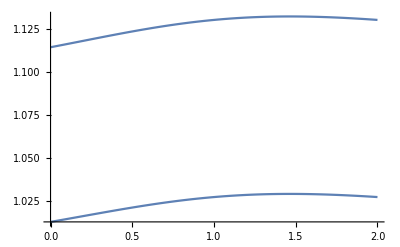

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
SetDirectory[NotebookDirectory[]];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gPlots3D`"];
Needs["gSphericalCap`"];

representPt={2,1};
groundPt={0,0};
lightPt={-1,1};
viewDir[wallY_]:=Normalize[groundPt-{2,wallY}];
lightDir[wallY_]:=Normalize[lightPt-{2,wallY}];
halfDir[wallY_]:=Normalize[(viewDir[wallY]+lightDir[wallY])/2];
p1=Plot[1/Dot[halfDir[wallY],viewDir[wallY]],{wallY,0,2}];
p2=Plot[1.1/Dot[halfDir[wallY],viewDir[wallY]],{wallY,0,2}];
Show[p1,p2,PlotRange->All]
```

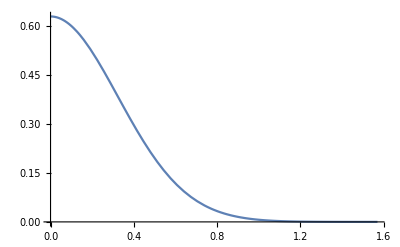

```mathematica
testProductIntegral[{inP1_,λ1_,μ1_},{inP2_,λ2_,μ2_},dotP_]:=Module[
	{p1,p2,λ3,c1,c2},
	p1=Normalize[inP1];
	p2=Normalize[inP2];
	
	c1=λ1*λ2/(λ1+λ2);
	(*c2=Dot[p1,p2];*)	
c2=dotP;
	λ3=λ1+λ2-c1*(1-c2);
	
	μ1*μ2*(2π)/λ3 Exp[c1*(c2-1)]
];

testProduct[{p1_,λ1_,μ1_},{p2_,λ2_,μ2_},dotP_]:=Module[
	{p3,λ3,μ3},
	
	λ3=(λ1+λ2)-(λ1*λ2/(λ1+λ2))*(1-dotP);
	p3=(λ1*p1+λ2*p2)/λ3;
	μ3=Exp[λ3-(λ1+λ2)];
	
	{p3,λ3,μ3}
];

sg3=testProductIntegral[{{1,1,1},λ1,μ1},{{-1,-1,1},λ2/VoH,μ2},VoL];
sg31=sg3/.{λ1->5,λ2->5,μ1->1,μ2->1};
Plot3D[sg31,{VoL,0,1},{VoH,0,1}];
(*sg32=sg31/.{VoL->Cos[2θ],VoH->Cos[θ+x]};
sg33=sg32/.{θ->π/8};
p31=Plot[sg33,{x,-3π/4,π/4}];*)
sg32=sg31/.{VoL->Cos[2θ],VoH->Cos[θ]};
p31=Plot[sg32,{θ,0,π/2}]

sg3a=sg3/.{μ1->1,μ2->1};
sg3b=sg3a/.{VoL->(2Cos[θ]^2-1),VoH->Cos[θ]};
```

```mathematica
sg4a[λ1_,λ2_,θ_]:=Block[{},(λ1 λ2 (-2+2 Cos[θ]^2) Sec[θ])/(λ1+λ2 Sec[θ])];

Manipulate[
Plot3D[(λ1 λ2 (-2+2 Cos[θ]^2) Sec[θ])/(λ1+λ2 Sec[θ]),{λ1,5,100},{λ2,5,50}],
{{θ,π/4},0.0001,1.57}]
π/2-0.0001
```

1.5707

```mathematica
theta2=ArcTan[Tan[theta1]*ax/(ax+t)];
phi2=phi1;
detH=Det[D[{theta2,phi2},{{theta1,phi1}}]];
detH;
(*detH1=(s* Sec[theta1]^2)/(1+s^2*Tan[theta1]^2);*)
detH2=detH/.{ax->Sin[theta1]};
detH3=FullSimplify@detH2;
detH3
detH4=detH3/.{theta1->π/4};
(*detH5=Series[detH4,{t,0,5}]*)
Plot[{detH4,sgPolar[ArcSin[t/5],20.878,1]},{t,0,1},PlotStyle->{Green,Blue}];

(*FindMinimum[NIntegrate[Abs[detH4-sgPolar[ArcSin[t/5],myX,1]],{t,0,1},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->1],
	 {myX,50}
]*)

FindMinimum[
	{
	NIntegrate[Abs[detH3-sgPolar[ArcSin[t/5],a+b/Tan[theta1],1]],
	{t,0,1},{theta1,0.1,π/4},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->1]
      },
	 {a,50},{b,1}
];

Manipulate[
Plot[{(Sec[theta1] (t+Sin[theta1]) Tan[theta1])/(t^2+2 t Sin[theta1]+Tan[theta1]^2),
	sgPolar[ArcSin[t/5],Max[(-39.107+59.852/Tan[theta1]),sgMinLambda],1]},
	{t,0,2},PlotStyle->{Green,Blue}],
	{theta1,0.01,π/2-0.01}
];

(*Solve[-58+33/Tan[theta1/2]==sgMinLambda,theta1]*)

Plot[{1/Tan[theta1/2]},
	{theta1,0.01,π/2},PlotStyle->{Blue}];
```

(Sec[theta1] (t+Sin[theta1]) Tan[theta1])/(t^2+2 t Sin[theta1]+Tan[theta1]^2)

NIntegrate::inumr: The integrand Abs[-ⅇ^((-1+√Plus[«2»]) (a+b Cot[«1»]))+(Sec[theta1] (t+Sin[theta1]) Tan[theta1])/(t^2+2 t Sin[theta1]+Tan[theta1]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand Abs[-1. ⅇ^((-1+√Plus[«2»]) (a+b Cot[«1»]))+(Sec[theta1] (t+Sin[theta1]) Tan[theta1])/(t^2+2. t Sin[theta1]+Tan[theta1]^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0723198,{a→-39.1072,b→59.8524}}

```mathematica
detH6=(Sec[thetaV] (t+Sin[thetaV]) Tan[thetaV])/(t^2+2 t Sin[thetaV]+Tan[thetaV]^2)*(Sec[thetaL] (t+Sin[thetaL]) Tan[thetaL])/(t^2+2 t Sin[thetaL]+Tan[thetaL]^2);
FindMinimum[
	{
	NIntegrate[Abs[detH6-sgPolar[ArcSin[t],a+b/(Tan[thetaV]*Tan[thetaL]),1]],
	{t,0,1},{thetaV,0.1,π/4},{thetaL,0.1,π/4},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->1]
      },
	 {a,50},{b,1}
];
```

NIntegrate::inumr: The integrand Abs[-ⅇ^((-1+√Plus[«2»]) (a+b Cot[«1»] Cot[«1»]))+(Sec[thetaL] Sec[thetaV] (t+Sin[thetaL]) (t+Sin[thetaV]) Tan[thetaL] Tan[thetaV])/((t^2+2 t Sin[thetaL]+Tan[thetaL]^2) (t^2+2 t Sin[thetaV]+Tan[thetaV]^2))] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand Abs[-1. ⅇ^((-1+√Plus[«2»]) (a+b Cot[«1»] Cot[«1»]))+(Sec[thetaL] Sec[thetaV] (t+Sin[thetaL]) (t+Sin[thetaV]) Tan[thetaL] Tan[thetaV])/((t^2+2. t Sin[thetaL]+Tan[thetaL]^2) (t^2+2. t Sin[thetaV]+Tan[thetaV]^2))] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 1.10294×10^8 and 5.34293×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0583333,{a→-1.80962,b→3.28658}}

(ⅇ^(-((-1+dotP) l1 l2)/(l1+l2)+(a b (-1+dotP) l1 l2)/(a l1+b l2)) ((dotP l1 l2)/(√(l1^2+l2^2))+√(l1^2+l2^2)))/((a b dotP l1 l2)/(√(a^2 l1^2+b^2 l2^2))+√(a^2 l1^2+b^2 l2^2))

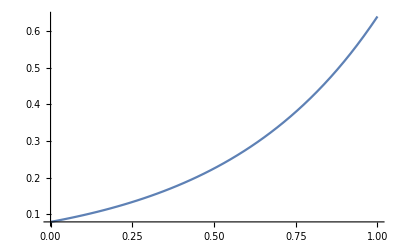

```mathematica
ClearAll[l1,l2,l3,dotP,a,b,f1,f2,f3];
l3[l1_,l2_]:=√(l1^2+l2^2)+(l1*l2*dotP)/(√(l1^2+l2^2));
(*l3[l1_,l2_]:=l1+l2+(l1*l2*dotP)/(l1+l2);*)
f1[l1_,l2_]:=(2π)/l3[l1,l2] Exp[(l1*l2)/(l1+l2)(dotP-1)];
f1[l1,l2];
f2[l1_,l2_,a_,b_]:=f1[l1*a,l2*b]/f1[l1,l2];
f2[l1,l2,a,b]
f3[a_,b_]:=f2[100,10,a,b];
Plot[f3[1.6,1.2],{dotP,0,1}]
```

```mathematica
Exp[-5]//N
```

0.00673795

```mathematica
(*$Assumptions=(p0|p|v)∈Vectors[1,Reals];
$Assumptions=(d)∈Vectors[1,Reals];
x1=Normalize[{x0-p0,x1-p1,x2-p2}];
x2=Normalize[{x0-p0+d,x1-p1,x2-p2}];
x3=Normalize[x-d];
Series[x2,{d,0,1}];*)

p0+d*v;
p0+d*(p0-n);
Sqrt[1+d^2+2d*Dot[p0,v]];
Sqrt[1+d^2+2d*z];
Series[Sqrt[1+d^2+2d*z],{d,0,2}];
Series[Sqrt[a^2+b^2+2*a*b*z],{z,0,1}]
```

√(a^2+b^2)+(a b z)/(√(a^2+b^2))+O[z]^2

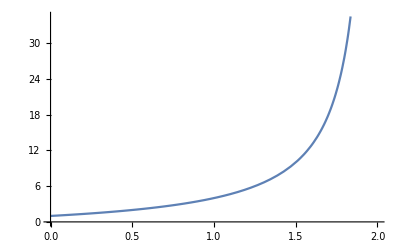

```mathematica
plotFunc12[k_]:=√2(1+k)/(√2-k/(√2));
Plot[plotFunc12[k],{k,0,2}]
```

√(l1^2+l2^2)+(l1 l2 dotP)/(√(l1^2+l2^2))+O[dotP]^2

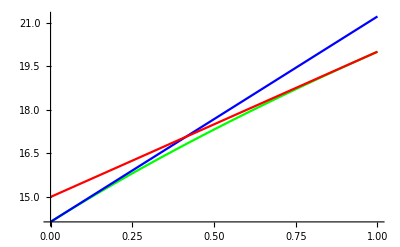

```mathematica
Series[Sqrt[l1^2+l2^2+2*l1*l2*dotP],{dotP,0,1}]
Plot[{(Sqrt[l1^2+l2^2+2*l1*l2*dotP])/.{l1->10,l2->10},
	(√(l1^2+l2^2)+(l1 l2 dotP)/(√(l1^2+l2^2)))/.{l1->10,l2->10},
	((l1+l2)-(l1*l2)/(l1+l2)(1-dotP))/.{l1->10,l2->10}},
	{dotP,0,1},
	PlotStyle->{Green,Blue,Red}]
```

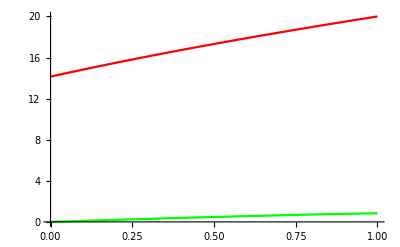

```mathematica
Plot[{Sqrt[l1^2+l2^2+2*l1*l2*dotP]/.{l1->10,l2->10},Sin[dotP]},{dotP,0,1},PlotStyle->{Red,Green}]
```